# Spatial ARGs

```mathematica
ClearAll
```

ClearAll

#### Rough Work -

```mathematica
f1[x_] := PDF[NormalDistribution[μ1,σ1],x];
f2[x_] := PDF[NormalDistribution[μ2,σ2],x];
f3[x_] := PDF[NormalDistribution[μ3,σ3],x];
Integrate[f1[x]*f2[x]*f3[x],{x,-∞,∞},Assumptions->{σ1>0,σ2>0,σ3>0}]
%/.{μ1->0,μ2->0,μ3->0}
```

(ⅇ^(-(-2 μ1 μ3 σ2^2+μ3^2 (σ1^2+σ2^2)+μ2^2 (σ1^2+σ3^2)+μ1^2 (σ2^2+σ3^2)-2 μ2 (μ3 σ1^2+μ1 σ3^2))/(2 (σ2^2 σ3^2+σ1^2 (σ2^2+σ3^2)))))/(2 π σ1 σ2 √(1/σ1^2+1/σ2^2+1/σ3^2) σ3)

1/(2 π σ1 σ2 √(1/σ1^2+1/σ2^2+1/σ3^2) σ3)

```mathematica
Integrate[f1[x]*f2[y-x],{x,-∞,∞},Assumptions->{σ1>0,σ2>0,σ3>0}]
```

(ⅇ^(-(-y+μ1+μ2)^2/(2 (σ1^2+σ2^2))))/(√(2 π) √(σ1^2+σ2^2))

#### Double Recombinant

```mathematica
f[x_,μ_,σ_] := PDF[NormalDistribution[μ,√σ],x];(*Defining the prob density function of a normal distribuion with mean μ and variance σ *)
MLE[loc_,CVmat_,n_]:=(ones = ConstantArray[1,{n,1}];Cinv=Inverse[CVmat];ahat = (Transpose[ones].Cinv.ones)^(-1)(Transpose[ones].Cinv.Transpose[loc])//Simplify;
z0= ahat[[1]][[1]];
d=Transpose[loc]-z0*ones;
Transpose[d].Cinv.d/n//Simplify
)
```

```mathematica
Pint = Integrate[f[x,0,t53]*f[y,0,t43]*f[x-y,0,t54]*f[z,0,t42]*f[z-y,0,t32],{x,-∞,∞},{y,-∞,∞},{z,-∞,∞},Assumptions->{t53>0,t43>0,t54>0,t32>0,t42>0}];(*Probability of all the meeting events happening*)
P=Integrate[f[y,0,t53]*f[x-y,0,t32]*f[z,0,t43]*f[y-z,0,t54]*f[x-y+z,0,t42],{y,-∞,∞},{z,-∞,∞},Assumptions->{t53>0,t43>0,t54>0,t32>0,t42>0}];
f52=P/Pint//Simplify;
Numerator[%]/.t32->T1-t42/.t54->T2-t53//Simplify
Collect[Denominator[%%]/.t32->T-t53/.t42->T-t54//Simplify,{t53,t54}]
```

√(T2 t43+T1 (T2+t43))

ⅇ^(-((-(t53+t54)^2+2 T (t43+t53+t54)) x^2)/(2 T (t53^2+t54^2-T (t43+t53+t54)))) √(2 π) √(T (-t53^2-t54^2+T (t43+t53+t54)))

```mathematica
V52=1/(2π f52^2)/.x->0;
Cbridges = {{t-t52+V52,0},{0,t}}/.t32->t52-t53/.t42->t52-t54/.t54->t53-t43/.t43->x t53/.t53->y t52//Simplify ;
Cpaths = {{t,t-t42,t-t52,0},{t-t42,t,t-t53,0},{t-t52,t-t53,t,0},{0,0,0,t}}/.t42->t52-t54/.t54->t53-t43/.t43->x t53/.t53->y t52//Simplify;
%%//Simplify//MatrixForm
%%//Simplify//MatrixForm
```

(t+(2 (t52+t52 (-1+x) y))/(-4+(-2+x)^2 y) | 0
0 | t)

(t | t+t52 (-1+y-x y) | t-t52 | 0
t+t52 (-1+y-x y) | t | t-t52 y | 0
t-t52 | t-t52 y | t | 0
0 | 0 | 0 | t)

```mathematica
SigBridge=MLE[{{x0,x1}},Cbridges,2];
Collect[0.5(x0-x1)^2/SigBridge[[1]][[1]]/.t52->z t,{t,z}]
SigPaths=MLE[{{x0,x0,x0,x1}},Cpaths,4]*4/2;
Collect[0.5(x0-x1)^2/SigPaths[[1]][[1]]/.t52->z t,{t,z}]
(*z = Length of the whole loop / Length of Branch, y = Length of subloop/ Length of whole loop,
x = Length of shared path/Length of subloop. Further z(1+(-1+x)y) = z - zy + xyz = [Len(Loop)-Len(SubLoop)+Len(SharedPath)]/Len(Branch)*)
```

t (2.+(2. (1+(-1+x) y) z)/(-4+(-2+x)^2 y))

t (2.+(2. (1+(-1+x) y) z)/(-4+(-2+x)^2 y))

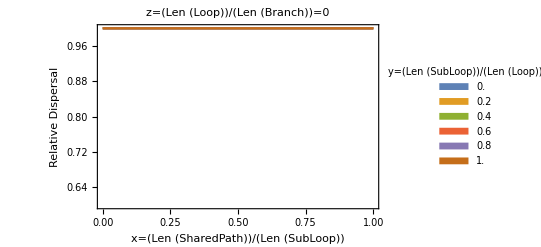

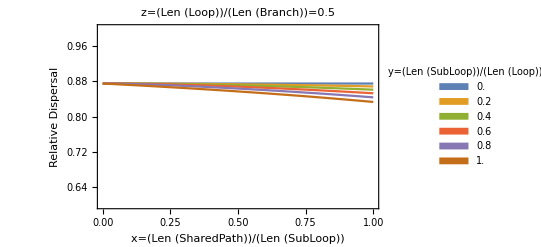

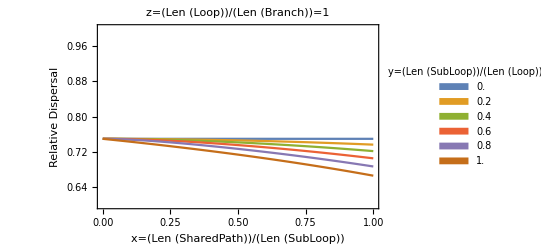

```mathematica
Sig[a_,b_,c_]:=(x0-x1)^2/(4*SigBridge)/.t52->z t/.t->1/.x->a/.y->b/.z->c;
Plot[Evaluate[Table[Sig[x,y,0],{y,0,1,0.2}]],{x,0,1},PlotLegends->Placed[SwatchLegend[Range[0,1,0.2],LegendLabel->"y=(Len (SubLoop))/(Len (Loop))"],Right],Frame->{True,True,False,False},FrameLabel->{"x=(Len (SharedPath))/(Len (SubLoop))","Relative Dispersal"},PlotLabel->"z=(Len (Loop))/(Len (Branch))=0",PlotRange->{Automatic,{0.6,1}}]
Plot[Evaluate[Table[Sig[x,y,0.5],{y,0,1,0.2}]],{x,0,1},PlotLegends->Placed[SwatchLegend[Range[0,1,0.2],LegendLabel->"y=(Len (SubLoop))/(Len (Loop))"],Right],Frame->{True,True,False,False},FrameLabel->{"x=(Len (SharedPath))/(Len (SubLoop))","Relative Dispersal"},PlotLabel->"z=(Len (Loop))/(Len (Branch))=0.5",PlotRange->{Automatic,{0.6,1}}]
Plot[Evaluate[Table[Sig[x,y,1],{y,0,1,0.2}]],{x,0,1},PlotLegends->Placed[SwatchLegend[Range[0,1,0.2],LegendLabel->"y=(Len (SubLoop))/(Len (Loop))"],Right],Frame->{True,True,False,False},FrameLabel->{"x=(Len (SharedPath))/(Len (SubLoop))","Relative Dispersal"},PlotLabel->"z=(Len (Loop))/(Len (Branch))=1",PlotRange->{Automatic,{0.6,1}}]
```

#### Compound Single Recombinant Event

```mathematica
ClearAll
```

ClearAll

```mathematica
P = Integrate[f[x,0,t43]*f[y,0,t32]*f[x+y,0,t42],{x,-∞,∞},{y,-∞,∞},Assumptions->{t32>0,t43>0,t42>0}]//Simplify
P42num=Integrate[f[y,0,t43]*f[x-y,0,t32]*f[x,0,t42],{y,-∞,∞},Assumptions->{t32>0,t43>0,t42>0}]//Simplify
P43num=Integrate[f[x,0,t43]*f[x-y,0,t32]*f[y,0,t42],{y,-∞,∞},Assumptions->{t32>0,t43>0,t42>0}]//Simplify
P4342=Simplify[f[y,0,t43]*f[x-y,0,t32]*f[x,0,t42],Assumptions->{t32>0,t43>0,t42>0}]//Simplify
```

1/(√(2 π) √(t32+t42+t43))

(ⅇ^(-((t32+t42+t43) x^2)/(2 t42 (t32+t43))))/(2 π √(t42 (t32+t43)))

(ⅇ^(-((t32+t42+t43) x^2)/(2 (t32+t42) t43)))/(2 π √((t32+t42) t43))

(ⅇ^(1/2 (-x^2/t42-(x-y)^2/t32-y^2/t43)))/(2 √2 π^(3/2) √(t32 t42 t43))

```mathematica
fjint[x_,y_]:=f[x,0,t42]*f[y,0,t43]*f[x-y,0,t32]//Simplify;
fjint[x,y]
```

(ⅇ^(1/2 (-x^2/t42-(x-y)^2/t32-y^2/t43)))/(2 √2 π^(3/2) √t32 √t42 √t43)

```mathematica
Ctemp = {{1/t42+1/t32,-1/t32},{-1/t32,1/t43+1/t32}};
Ctemp = Inverse[Ctemp];
Cbridges = {{%[[1]][[1]]+t-t42,%[[1]][[2]] } ,{%[[1]][[2]],%[[2]][[2]]+t-t43}}/.t32->t42-t43/.t43-> y t42/.t42-> x t//Simplify;
Cpaths ={{t,t-t42,0},{t-t42,t,t43},{0,t43,t}}/.t32->t42-t43/.t43-> y t42/.t42-> x t//Simplify;
SigBridge=MLE[{{x0,x1}},Cbridges,2];
0.5(x0-x1)^2/SigBridge[[1]][[1]]
SigPaths=MLE[{{x0,x0,x1}},Cpaths,3]*3/2;
0.5(x0-x1)^2/SigPaths[[1]][[1]]
```

-0.5 t (-4+x (1+y)^2)

-0.5 t (-4+x (1+y)^2)

#### Compound Double Recombination Event.

```mathematica
ClearAll
```

ClearAll

```mathematica
fjint[w_,x_,y_,z_]:=f[w,0,t63]*f[x,0,t65]*f[y,0,t43]*f[w-x-y,0,t54]*f[z,0,t52]*f[x+y+z-w,0,t42];
fjint[w,x,y,z]//Simplify
```

(ⅇ^(1/2 (-w^2/t63-x^2/t65-y^2/t43-(-w+x+y)^2/t54-z^2/t52-(-w+x+y+z)^2/t42)))/(8 π^3 √t42 √t43 √t52 √t54 √t63 √t65)

```mathematica
Ctempinv={{1/t63+1/t54+1/t42,-1/t54-1/t42,-1/t54-1/t42,-1/t42},{-1/t54-1/t42,1/t65+1/t54+1/t42,1/t54+1/t42,1/t42},{-1/t54-1/t42,1/t54+1/t42,1/t43+1/t54+1/t42,1/t42},{-1/t42,1/t42,1/t42,1/t42+1/t52}};
%//MatrixForm
Ctemp = Inverse[Ctempinv];
Cbridges={{Ctemp[[1]][[1]]+t-t63,Ctemp[[1]][[2]]+Ctemp[[1]][[4]]},{Ctemp[[1]][[2]]+Ctemp[[1]][[4]],Ctemp[[2]][[2]]+Ctemp[[4]][[4]]+2Ctemp[[4]][[2]]+t-t65-t52}}/.t43->t63-t65-t54/.t42->t52-t54/.t65->z1 t63/.t54->z2 t63/.t52->y t/.t63->x t;
Cpaths = {{t,t-t63,0,0},{t-t63,t,t65+t54,t65},{0,t65+t54,t,t-t52},{0,t65,t-t52,t}}/.t43->t63-t65-t54/.t42->t52-t54/.t65->z1 t63/.t54->z2 t63/.t52->y t/.t63->x t;
SigBridge=MLE[{{x0,x1}},Cbridges,2];
0.5(x0-x1)^2/SigBridge[[1]][[1]]//Simplify
SigPaths=MLE[{{x0,x0,x1,x1}},Cpaths,4]*4/2;
0.5(x0-x1)^2/SigPaths[[1]][[1]]
```

(1/t42+1/t54+1/t63 | -1/t42-1/t54 | -1/t42-1/t54 | -1/t42
-1/t42-1/t54 | 1/t42+1/t54+1/t65 | 1/t42+1/t54 | 1/t42
-1/t42-1/t54 | 1/t42+1/t54 | 1/t42+1/t43+1/t54 | 1/t42
-1/t42 | 1/t42 | 1/t42 | 1/t42+1/t52)

-(2. t (y^2+x z2^2+y (-4+x (1+z1) (1+z1+z2))))/(4 y-x z2^2)

-(2. t (y^2+x z2^2+y (-4+x (1+z1) (1+z1+z2))))/(4 y-x z2^2)

```mathematica
P63num = Integrate[fjint[w,x,y,z],{x,-∞,∞},{y,-∞,∞},{z,-∞,∞},Assumptions->{t63>0,t65>0,t43>0,t54>0,t52>0,t42>0}]
```

(ⅇ^(-((t52 t54+t43 (t52+t54)+t52 t63+t54 t63+t52 t65+t54 t65+t42 (t43+t54+t63+t65)) w^2)/(2 t63 (t52 t54+t43 (t52+t54)+t52 t65+t54 t65+t42 (t43+t54+t65)))))/(2 √2 π^(3/2) √(t63 (t52 t54+t43 (t52+t54)+t52 t65+t54 t65+t42 (t43+t54+t65))))

```mathematica
P=Integrate[fjint[w,x,y,z],{w,-∞,∞},{x,-∞,∞},{y,-∞,∞},{z,-∞,∞},Assumptions->{t63>0,t65>0,t43>0,t54>0,t52>0,t42>0}]//Simplify
```

1/(2 π √(t52 t54+t43 (t52+t54)+t52 t63+t54 t63+t52 t65+t54 t65+t42 (t43+t54+t63+t65)))

```mathematica
1/(2π(P63num/P/.w->0)^2)
%-Ctemp[[1]][[1]]//Simplify
P65num=Integrate[fjint[w,x,y,z],{w,-∞,∞},{y,-∞,∞},{z,-∞,∞},Assumptions->{t63>0,t65>0,t43>0,t54>0,t52>0,t42>0}]
1/(2π(P65num/P/.x->0)^2)
%-Ctemp[[2]][[2]]//Simplify
```

(t63 (t52 t54+t43 (t52+t54)+t52 t65+t54 t65+t42 (t43+t54+t65)))/(t52 t54+t43 (t52+t54)+t52 t63+t54 t63+t52 t65+t54 t65+t42 (t43+t54+t63+t65))

0

(ⅇ^(-((t52 t54+t43 (t52+t54)+t52 t63+t54 t63+t52 t65+t54 t65+t42 (t43+t54+t63+t65)) x^2)/(2 (t52 t54+t43 (t52+t54)+t52 t63+t54 t63+t42 (t43+t54+t63)) t65)))/(2 √2 π^(3/2) √((t52 t54+t43 (t52+t54)+t52 t63+t54 t63+t42 (t43+t54+t63)) t65))

((t52 t54+t43 (t52+t54)+t52 t63+t54 t63+t42 (t43+t54+t63)) t65)/(t52 t54+t43 (t52+t54)+t52 t63+t54 t63+t52 t65+t54 t65+t42 (t43+t54+t63+t65))

0

```mathematica
P65num=Integrate[fjint[w,x,y,z],{w,-∞,∞},{y,-∞,∞},{x,-∞,∞},Assumptions->{t63>0,t65>0,t43>0,t54>0,t52>0,t42>0}]
1/(2π(P65num/P/.z->0)^2)
%-Ctemp[[4]][[4]]//Simplify
```

(ⅇ^(-((t52 t54+t43 (t52+t54)+t52 t63+t54 t63+t52 t65+t54 t65+t42 (t43+t54+t63+t65)) z^2)/(2 t52 (t54 (t43+t63+t65)+t42 (t43+t54+t63+t65)))))/(2 √2 π^(3/2) √(t52 (t54 (t43+t63+t65)+t42 (t43+t54+t63+t65))))

(t52 (t54 (t43+t63+t65)+t42 (t43+t54+t63+t65)))/(t52 t54+t43 (t52+t54)+t52 t63+t54 t63+t52 t65+t54 t65+t42 (t43+t54+t63+t65))

0

```mathematica
P65num=Integrate[w*x*fjint[w,x,y,z],{w,-∞,∞},{x,-∞,∞},{y,-∞,∞},{z,-∞,∞},Assumptions->{t63>0,t65>0,t43>0,t54>0,t52>0,t42>0}]
```

((t42+t52+t54) t63 t65)/(2 π (t52 t54+t43 (t52+t54)+t52 t63+t54 t63+t52 t65+t54 t65+t42 (t43+t54+t63+t65))^(3/2))

```mathematica
P65num/P
Ctemp[[1]][[2]]-%//Simplify
```

((t42+t52+t54) t63 t65)/(t52 t54+t43 (t52+t54)+t52 t63+t54 t63+t52 t65+t54 t65+t42 (t43+t54+t63+t65))

0

```mathematica
C6352num=Integrate[w*z*fjint[w,x,y,z],{w,-∞,∞},{x,-∞,∞},{y,-∞,∞},{z,-∞,∞},Assumptions->{t63>0,t65>0,t43>0,t54>0,t52>0,t42>0}]
```

(t52 t54 t63)/(2 π (t52 t54+t43 (t52+t54)+t52 t63+t54 t63+t52 t65+t54 t65+t42 (t43+t54+t63+t65))^(3/2))

```mathematica
C6352num/P
Ctemp[[1]][[4]]-%//Simplify
```

(t52 t54 t63)/(t52 t54+t43 (t52+t54)+t52 t63+t54 t63+t52 t65+t54 t65+t42 (t43+t54+t63+t65))

0

#### Eigenvalue comparison for single compound recombination - Don’t Match

```mathematica
Cpaths = {{t,t20,0},{t20,t,t43},{0,t43,t}};
Cbridge = {{t42/2 +t20, t43/2},{t43/2,t43(2t42-t43)/(2t42) + t31}}
```

{{t20+t42/2,t43/2},{t43/2,t31+((2 t42-t43) t43)/(2 t42)}}

```mathematica
Eigenvalues[Cpaths/.{t20->t-t42,t31->t-t43,t43 ->(1-x) t42,t32->x t42}]//Simplify
```

{t,t-√(t^2-2 t t42+t42^2 (2-2 x+x^2)),t+√(t^2-2 t t42+t42^2 (2-2 x+x^2))}

```mathematica
Eigenvalues[Cbridge/.{t20->t-t42,t31->t-t43}/.{t43 ->(1-x) t42,t32->x t42}]//Simplify
```

{t,t-1/2 t42 (2-2 x+x^2)}

```mathematica
Clear[x1]
```

```mathematica
CM =  {  {(1-x/2)t, (1 - x/2 +- z)t, y t/2}, {(1 - x/2 +- z)t, (1-x/2)t, y t/2}, { y t/2, y t/2, (1 - y(x+y)/(2x))t} } 
%//MatrixForm
L = Transpose[{{l - d, l + d, l2}}]
Transpose[L].L
Simplify[Transpose[L].Inverse[CM].L]
```

{{t (1-x/2),t (1-x/2-z),(t y)/2},{t (1-x/2-z),t (1-x/2),(t y)/2},{(t y)/2,(t y)/2,t (1-(y (x+y))/(2 x))}}

(t (1-x/2) | t (1-x/2-z) | (t y)/2
t (1-x/2-z) | t (1-x/2) | (t y)/2
(t y)/2 | (t y)/2 | t (1-(y (x+y))/(2 x)))

{{-d+l},{d+l},{l2}}

{{(-d+l)^2+(d+l)^2+l2^2}}

{{(2 (d^2/z-(2 l l2 x y+l^2 (x (-2+y)+y^2)+l2^2 x (-2+x+z))/(x^2 (-2+y)+x (-2+y) (-2+z)+y^2 (-2+z))))/t}}

```mathematica
CM1 =  {  {t, (1 - z)t, 0}, {(1- z)t, t,0}, {0, 0, t} } ;
CM2 =  {  {(1-y)t, (1 -y- z)t, 0}, {(1- y-z)t, (1-y)t,0}, {0, 0,(1-y)t} } ;
CM3 =  {  {t, (1- z)t, y t}, {(1-z)t, t,y t}, {y t, y t,(1-y)t} } ;
%//MatrixForm
L = Transpose[{{l - d, l + d, l2}}];
Simplify[Transpose[L].Inverse[CM1].L]
Simplify[Transpose[L].Inverse[CM2].L]
Simplify[Transpose[L].Inverse[CM3].L]
```

(t | t (1-z) | t y
t (1-z) | t | t y
t y | t y | t (1-y))

{{(l2^2-(2 l^2)/(-2+z)+(2 d^2)/z)/t}}

{{(-l2^2/(-1+y)+(2 d^2)/z-(2 l^2)/(-2+2 y+z))/t}}

{{-((2 l^2 (-1+y)+4 l l2 y+l2^2 (-2+z)) z+2 d^2 (-2+2 y^2-y (-2+z)+z))/(t (2-2 y^2+y (-2+z)-z) z)}}

#### Variance and Covariance of Internal nodes is indifferent to the choice of internal path

```mathematica
Sp = {{t,t13,0},{t13, t, t46},{0, t46, t}}/. t->t1+t2+t3/.t13->t1/.t46->t3;
Sp//MatrixForm
```

(t1+t2+t3 | t1 | 0
t1 | t1+t2+t3 | t3
0 | t3 | t1+t2+t3)

```mathematica
R = {{1,0},{0,1},{1,0}};
R//MatrixForm
```

(1 | 0
0 | 1
1 | 0)

```mathematica
l = {{l1},{l1},{l2}}
SpInv = Inverse[Sp]//Simplify;
mu = Inverse[Transpose[R].SpInv.R].Transpose[R].SpInv.l//Simplify
sb = {{0},{t3},{t3}}
```

{{l1},{l1},{l2}}

{{(l1+l2)/2},{(l2 (t1-t3)+l1 (t1+2 t2+3 t3))/(2 (t1+t2+t3))}}

{{0},{t3},{t3}}

Internal Node 3 Location and its covariance with Node 4 using Path to root 5

```mathematica
sa = {{t2+t3},{0},{0}};
mu[[1,1]]+Transpose[sa].SpInv.(l-R.mu)//Simplify
a1 = Transpose[sa].SpInv.sa//Factor
CV =0-Transpose[sa].SpInv.sb//Simplify
```

{{(l2 t1+l1 (t1+2 (t2+t3)))/(2 (t1+t2+t3))}}

{{((t1+t2) (t2+t3)^2 (t1+t2+2 t3))/((t1+t2+t3) (2 t1 t2+t2^2+2 t1 t3+2 t2 t3))}}

{{(t1 (t1+t2) t3 (t2+t3))/((t1+t2+t3) (2 t1 (t2+t3)+t2 (t2+2 t3)))}}

Internal Node 3 Location and its covariance with Node 4 using Path to root 6.

```mathematica
sa={{0},{t2+ t3},{t3}}
mu[[2,1]]+Transpose[sa].SpInv.(l-R.mu)//Simplify
a2 =Transpose[sa].SpInv.sa//Factor
CV =t3-Transpose[sa].SpInv.sb//Simplify
```

{{0},{t2+t3},{t3}}

{{(l2 t1+l1 (t1+2 (t2+t3)))/(2 (t1+t2+t3))}}

{{((t1+t2) (t2+t3)^2 (t1+t2+2 t3))/((t1+t2+t3) (2 t1 t2+t2^2+2 t1 t3+2 t2 t3))}}

{{(t1 (t1+t2) t3 (t2+t3))/((t1+t2+t3) (2 t1 (t2+t3)+t2 (t2+2 t3)))}}

(t1+t2+t3) (2 t1 t2+t2^2+2 t1 t3+2 t2 t3)